```mathematica
SetDirectory[NotebookDirectory[]];
```

## Explicit functions

```mathematica
names={"Constant","Linear","Quadratic","Cubic","Sine","Inverse Sine","Tangent","Inverse tangent","Positive exponential","Negative exponential","Log"};
equations = {0,x,x^2,x^3, Sin[x],ArcSin[x],Tan[x],ArcTan[x],E^x, E^(-x),Log[x]};
TraditionalForm[equations]
```

{0,x,x^2,x^3,sin(x),sin^-1(x),tan(x),tan^-1(x),ⅇ^x,ⅇ^-x,log(x)}

```mathematica
plots = Table[Plot[i,{x,0,10},PlotTheme->"Web"], {i,equations}]; (* You can remove the semicolon to see what any expression is doing *)
```

```mathematica
export = Rasterize[Grid[Transpose[{names, equations, plots}], Frame->All]]
Export["Table 1.png",export]
```

-Graphics-

Table 1.png

## Conic Sections

```mathematica
conics = {"Circle"-> x^2+y^2-4,"Ellipse" -> x^2+3y^2-9, "Parabola" -> x^2-y, "Hyperbola" -> y^2-x^2-1}
```

{Circle→-4+x^2+y^2,Ellipse→-9+x^2+3 y^2,Parabola→x^2-y,Hyperbola→-1-x^2+y^2}

```mathematica
tConics := Transpose[conics/.Rule->List]
```

```mathematica
ContourPlot[tConics[[2]][[1]]==0, {x,-3,3}, {y,-3,3}];
```

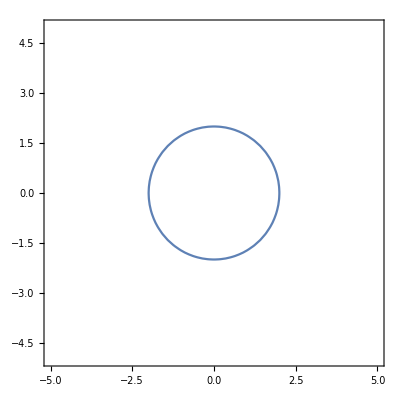
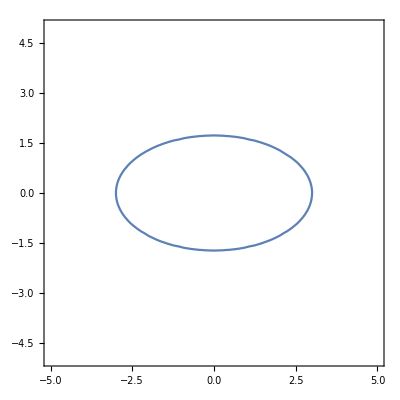
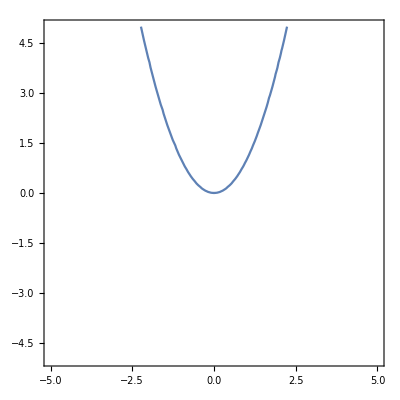
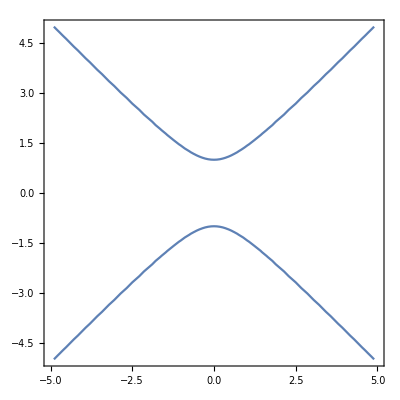

```mathematica
imPlots = Table[ContourPlot[i==0,{x,-5,5}, {y,-5,5}], {i,tConics[[2]]}]
```

```mathematica
export = Rasterize[Grid[Transpose[{tConics[[1]], Table[TraditionalForm[i==0],{i,tConics[[2]]}], imPlots}], Frame->All]]
Export["Table 2.png",export]
```

-Graphics-

Table 2.png

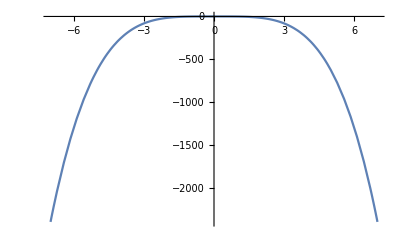
-Graphics--Graphics-

```mathematica
Overlay[Reverse[{Plot[-x^4,{x,-7,7}],ImageResize[Import["sketches/AppleTop.png"],400]}]]
```